## Introduction

## Analysis in (sum, diff) coordinates E = 0

### Define equations

```mathematica
Clear[b,j,k]
es={
2e-b Cos[xp] Sin[xm],
-b Sin[xp] Cos[xm]-j/2 Sin[2 xm]Cos[2 θm],
2e-b Cos[θp] Sin[θm],
-b Sin[θp] Cos[θm]-k/2 Sin[2 θm]Cos[2xm]
}/.e->0/.b->1;
TableForm[es]
```

-Cos[xp] Sin[xm]
-1/2 j Cos[2 θm] Sin[2 xm]-Cos[xm] Sin[xp]
-Cos[θp] Sin[θm]
-1/2 k Cos[2 xm] Sin[2 θm]-Cos[θm] Sin[θp]

```mathematica
Clear[b,k]
fp=Solve[(es)=={0,0,0,0},{xp,xm,θp,θm}];
TableForm[fp]
```

1
 |  |  |  |

### Bifurcations

#### Saddle node

```mathematica
J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]};
temp=Flatten[{es,Det[J]}];
sn=Solve[temp==0];
Length[sn]
```

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is -ArcCos[Cos[θp]] == 0.

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is -ArcCos[Cos[θm]] == 0.

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is -ArcCos[Cos[xp]] == 0.

General::stop: Further output of Solve::incnst will be suppressed during this calculation.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

72

```mathematica
DeleteDuplicates[{j,k}/.sn]//TableForm
```

-1 | k
1 | k
j | -1
j | 1

Ok. So there are some saddle nodes at ±1

#### Hopf

```mathematica
J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]};
temp=Flatten[{es,Tr[J]}];
hopf=Solve[temp==0];
Length[hopf]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

49

```mathematica
hopf[[1;;5]]//TableForm
```

j→-2-k | xm→-π/2 | xp→-π/2 | θm→0 | θp→0
j→-2-k | xm→-π/2 | xp→-π/2 | θm→-π | θp→0
j→-2-k | xm→-π/2 | xp→-π/2 | θm→π | θp→0
j→-2-k | xm→π/2 | xp→π/2 | θm→0 | θp→0
j→-2-k | xm→π/2 | xp→π/2 | θm→-π | θp→0

```mathematica
DeleteDuplicates[{j,k}/.hopf]//TableForm
```

-2-k | k
2-k | k
j | -4-j
j | -2-j
j | 2-j
j | 4-j
j | -j

So here are the hopf

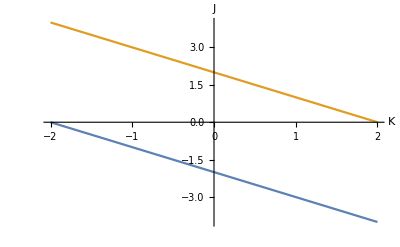

```mathematica
Plot[{-2-k,2-k},{k,-2,2},AxesLabel->{Style["K",Italic],Style["J",Italic]},LabelStyle->15]
```

```mathematica
hopf[[1]]
```

{j→-2-k,xm→-π/2,xp→-π/2,θm→0,θp→0}

#### Takens bogdanov

```mathematica
J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]};
temp=Flatten[{es,Det[J],Tr[J]}];
tb=Solve[temp==0];
Length[tb]
```

120

```mathematica
DeleteDuplicates[{j,k}/.tb]//TableForm
```

-3 | -1
-1 | -3
-1 | -1
-1 | 1
1 | -1
1 | 1
1 | 3
3 | 1
-3 √(3/2) | 3 √(3/2)
3 √(3/2) | -3 √(3/2)
-ⅈ/(√2) | ⅈ/(√2)
ⅈ/(√2) | -ⅈ/(√2)

Interesting. So there’s a bunch of TB points here!

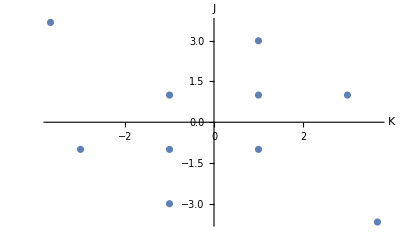

```mathematica
ListPlot[DeleteDuplicates[{j,k}/.tb],AxesLabel->{Style["K",Italic],Style["J",Italic]},LabelStyle->15]
```

#### Plot

```mathematica
DeleteDuplicates[{j,k}/.hopf]//TableForm
```

-2-k | k
2-k | k
j | -4-j
j | -2-j
j | 2-j
j | 4-j
j | -j

```mathematica
Solve[k==4-j,j]
```

{{j→4-k}}

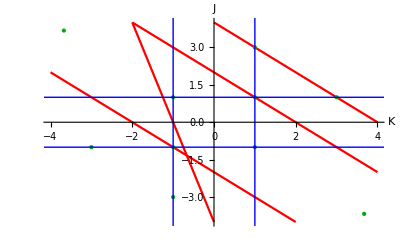

```mathematica
p1=Plot[{-2-k,2-k,-4-4k,4-k},{k,-4,4},AxesLabel->{Style["K",Italic],Style["J",Italic]},LabelStyle->20,PlotRange->{-4,4},PlotStyle->{Red},
Epilog->{
Blue,
Line[{{-1,-10},{-1,10}}],
Line[{{1,-10},{1,10}}],
Line[{{-10,1},{10,1}}],
Line[{{-10,-1},{10,-1}}]
}
];
pTB=ListPlot[DeleteDuplicates[{j,k}/.tb],AxesLabel->{Style["K",Italic],Style["J",Italic]},LabelStyle->20,PlotStyle->{PointSize[Large],Darker[Green]}];
Show[{p1,pTB}]
```

1. Blue are saddle nodes
2. Red are hopf’s
3. Green are TB ponts

### Solve for fp

```mathematica
Clear[b,k]
fp=Solve[(es/.b->0.5)=={0,0,0,0},{xp,xm,θp,θm}];
TableForm[fp]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

1
 |  |  |  |

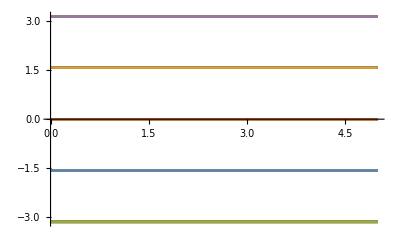

```mathematica
Plot[xp/.fp/.{C[1]->0,C[2]->0,C[3]->0,b->0.5,k->k1}//Evaluate,{k1,0,5}]
```

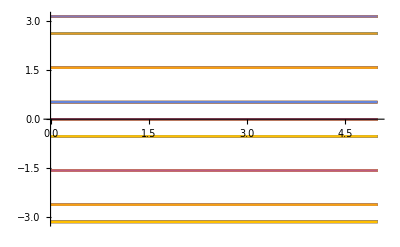

```mathematica
Plot[xm/.fp/.{C[1]->0,C[2]->0,C[3]->0,b->0.5,k->k1}//Evaluate,{k1,0,5}]
```

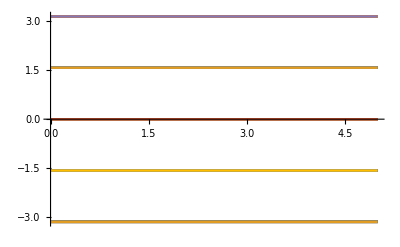

```mathematica
Plot[θp/.fp/.{C[1]->0,C[2]->0,C[3]->0,b->0.5,k->k1}//Evaluate,{k1,0,5}]
```

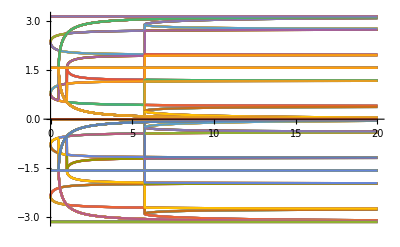

```mathematica
Plot[θm/.fp/.{C[1]->0,C[2]->0,C[3]->0,b->0.5,k->k1}//Evaluate,{k1,0,20}]
```

Interesting. Do we see this?

## Analysis in (sum, diff) coordinates E > 0 with J = K

### Define equations

```mathematica
Clear[b,j,k]
es={
2e-b Cos[xp] Sin[xm],
-b Sin[xp] Cos[xm]-j/2 Sin[2 xm]Cos[2 θm],
2e-b Cos[θp] Sin[θm],
-b Sin[θp] Cos[θm]-k/2 Sin[2 θm]Cos[2xm]
}/.b->1/.j->k;
TableForm[es]
```

2 e-Cos[xp] Sin[xm]
-1/2 k Cos[2 θm] Sin[2 xm]-Cos[xm] Sin[xp]
2 e-Cos[θp] Sin[θm]
-1/2 k Cos[2 xm] Sin[2 θm]-Cos[θm] Sin[θp]

```mathematica
Clear[b,k]
fp=Solve[(es)=={0,0,0,0},{xp,xm,θp,θm}];
TableForm[fp]
```

$Aborted

1
 |  |  |  |

### Bifurcations

#### Saddle node

```mathematica
J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]};
det=FullSimplify[Det[J]];
temp=Flatten[{es,det}];
sn=Solve[temp==0];
Length[sn]
```

Sin[xm] Sin[xp] (k Cos[2 xm] Cos[2 θm]-Sin[xm] Sin[xp]) (Cos[θm]^2 Cos[θp]^2+Sin[θm] Sin[θp] (k Cos[2 xm] Cos[2 θm]-Sin[θm] Sin[θp]))+Cos[xm]^2 (-4 k^2 Sin[xm]^3 Sin[xp] Sin[θm] Sin[2 θm]^2 Sin[θp]+Cos[xp]^2 (Cos[θm]^2 Cos[θp]^2+Sin[θm] Sin[θp] (k Cos[2 xm] Cos[2 θm]-Sin[θm] Sin[θp])))

```mathematica
DeleteDuplicates[{j,k}/.sn]//TableForm
```

-1 | k
1 | k
j | -1
j | 1

#### Hopf

```mathematica
J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]};
temp=Flatten[{es,Tr[J]}];
hopf=Solve[temp==0];
Length[hopf]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

258

```mathematica
cleanHopf=DeleteDuplicates[{k,e}/.hopf]//FullSimplify;
TableForm[cleanHopf]
```

0 | -1/2 √(Sin[xm]^2)
0 | 1/2 √(Sin[xm]^2)
-(Cos[xm] √(-1+2 Cos[xm]^2-Cos[xm]^6))/(√(-1+Cos[xm]^2+Cos[xm]^4) √Cos[2 xm] √(Sin[xm]^2)) | -(√(-1+Cos[xm]^2+Cos[xm]^4) √(Sin[xm]^2))/(2 √Cos[2 xm])
(Cos[xm] √(-1+2 Cos[xm]^2-Cos[xm]^6))/(√(-1+Cos[xm]^2+Cos[xm]^4) √Cos[2 xm] √(Sin[xm]^2)) | -(√(-1+Cos[xm]^2+Cos[xm]^4) √(Sin[xm]^2))/(2 √Cos[2 xm])
-(Cos[xm] √(-1+2 Cos[xm]^2-Cos[xm]^6))/(√(-1+Cos[xm]^2+Cos[xm]^4) √Cos[2 xm] √(Sin[xm]^2)) | (√(-1+Cos[xm]^2+Cos[xm]^4) √(Sin[xm]^2))/(2 √Cos[2 xm])
(Cos[xm] √(-1+2 Cos[xm]^2-Cos[xm]^6))/(√(-1+Cos[xm]^2+Cos[xm]^4) √Cos[2 xm] √(Sin[xm]^2)) | (√(-1+Cos[xm]^2+Cos[xm]^4) √(Sin[xm]^2))/(2 √Cos[2 xm])
-(√(Sin[2 θm]^2))/(2 √Cos[2 θm] √(Sin[θm]^2)) | -(√(-1+Cos[θm]^2+Cos[θm]^4) √(Sin[θm]^2))/(2 √Cos[2 θm])
(√(Sin[2 θm]^2))/(2 √Cos[2 θm] √(Sin[θm]^2)) | -(√(-1+Cos[θm]^2+Cos[θm]^4) √(Sin[θm]^2))/(2 √Cos[2 θm])
-(√(Sin[2 θm]^2))/(2 √Cos[2 θm] √(Sin[θm]^2)) | (√(-1+Cos[θm]^2+Cos[θm]^4) √(Sin[θm]^2))/(2 √Cos[2 θm])
(√(Sin[2 θm]^2))/(2 √Cos[2 θm] √(Sin[θm]^2)) | (√(-1+Cos[θm]^2+Cos[θm]^4) √(Sin[θm]^2))/(2 √Cos[2 θm])
0 | -Cos[θp]/2
-2 √(Sin[θp]^2) | -Cos[θp]/2
2 √(Sin[θp]^2) | -Cos[θp]/2
0 | Cos[θp]/2
-2 √(Sin[θp]^2) | Cos[θp]/2
2 √(Sin[θp]^2) | Cos[θp]/2

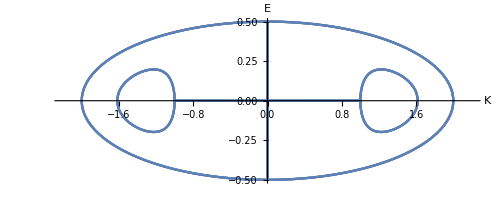

```mathematica
p1=ParametricPlot[cleanHopf[[1;;6]],{xm,-π,π},AxesLabel->{Style["K",18,Italic],Style["E",18,Italic]},LabelStyle->15,PlotRange->{{-2.2,2.2},Automatic}];
p2=ParametricPlot[cleanHopf[[6;;10]],{θm,-π,π},AxesLabel->{"K","E"},LabelStyle->15];
p3=ParametricPlot[cleanHopf[[11;;-1]],{θp,-π,π},AxesLabel->{"K","E"},LabelStyle->15];
p4=Show[{p1,p2,p3}]
```

#### Takens bogdanov

```mathematica
J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]};
temp=Flatten[{es,Det[J],Tr[J]}];
tb=Solve[temp==0];
Length[tb]
```

296

Let’s plot them along with the Hopf curves

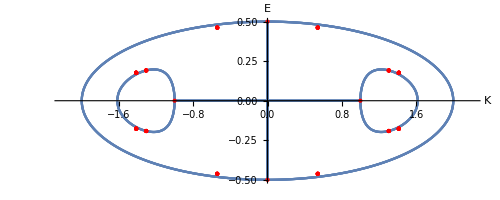

```mathematica
p5=ListPlot[DeleteDuplicates[{k,e}/.tb],AxesLabel->{Style["K",Italic],Style["E",Italic]},LabelStyle->15,PlotStyle->{Red,PointSize[Large]}];
Show[p4,p5]
```

That’s beautiful! I hope its genuine.

### Solve for fp

```mathematica
Clear[b,k]
fp=Solve[(es/.b->0.5)=={0,0,0,0},{xp,xm,θp,θm}];
TableForm[fp]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

1
 |  |  |  |

```mathematica
Plot[xp/.fp/.{C[1]->0,C[2]->0,C[3]->0,b->0.5,k->k1}//Evaluate,{k1,0,5}]
```

-Graphics-

```mathematica
Plot[xm/.fp/.{C[1]->0,C[2]->0,C[3]->0,b->0.5,k->k1}//Evaluate,{k1,0,5}]
```

-Graphics-

```mathematica
Plot[θp/.fp/.{C[1]->0,C[2]->0,C[3]->0,b->0.5,k->k1}//Evaluate,{k1,0,5}]
```

-Graphics-

```mathematica
Plot[θm/.fp/.{C[1]->0,C[2]->0,C[3]->0,b->0.5,k->k1}//Evaluate,{k1,0,20}]
```

-Graphics-

Interesting. Do we see this?

## E > 0